## Funciones

## Operadores

### Coin

```mathematica
-Graphics-;
```

```mathematica
n[α_,ϕ_]:={Sin[α]Cos[ϕ],Sin[α]Sin[ϕ],Cos[α]}
```

```mathematica
Paulis=PauliMatrix/@Range[3];
```

```mathematica
expCoin[θ_,α_,ϕ_]:=MatrixExp[(-ⅈ θ)/2.(n[α,ϕ].Paulis)]
```

```mathematica
Coin[θ_,α_,ϕ_,t_Integer]:=KroneckerProduct[SparseArray[Table[{i,i}->1.,{i,2 t+1}]],SparseArray[expCoin[θ,α,ϕ]]]
```

```mathematica
α=2 π/5;
ϕ=π;
t=1;
Coin[θ,α,ϕ,t]
```

SparseArray[…]

### Shift

```mathematica
Shift[t_Integer]:=SparseArray[Join[Table[{i,i+2},{i,Range[2,#-2,2]}],Table[{i,i-2},{i,Range[3,#,2]}]]->1.,{#,#}]&[2*(2*t+1)]
```

```mathematica
t=1;
Shift[t].{0,0,1,0,0,0}
```

{0.,0.,0.,0.,1.,0.}

### Unitaria

```mathematica
Unitary[θ_,α_,ϕ_,t_Integer]:=Shift[t].Coin[θ,α,ϕ,t]
```

```mathematica
α=2 π/5;
ϕ=π;
t=1;
Unitary[θ,α,ϕ,t]
```

SparseArray[…]

```mathematica
Unitary[paramsCoin_List,t_Integer]:=Module[{coinProduct},
coinProduct=Dot@@(Coin[##,t]&@@@Reverse[paramsCoin]);
Shift[t].coinProduct]
```

## Funciones cálculos

### Estados de la moneda

```mathematica
state0={1.,0.};
state1={0.,1.};
plusX=1/Sqrt[2]{1.,1.};
minusX=1/Sqrt[2]{1.,-1.};
plusY=1/Sqrt[2.]{1,ⅈ};
minusY=1/Sqrt[2.]{1,-ⅈ};
```

```mathematica
HVecs=N[Normalize/@Eigenvectors[HadamardMatrix[2]]];
HMinus=HVecs[[1]];
HPlus=HVecs[[2]];
```

### Estado aleatorio

```mathematica
QubitState[θ_,ϕ_]:={Cos[θ/2] ,Exp[I ϕ] Sin[θ/2] }
```

```mathematica
ClearAll@RandomQubitState
```

```mathematica
RandomQubitState[seed_:Automatic]:=Module[{x,y,z,θ,ϕ},If[seed=!=Automatic,SeedRandom[seed]];
{x,y,z}=RandomPoint[Sphere[]];
{θ,ϕ}={ArcCos[z],Sign[y] ArcCos[x/Sqrt[x^2+y^2]]};
{θ,ϕ,Cos[θ/2],Exp[I ϕ] Sin[θ/2]}]
```

```mathematica
RandomQubitState[123]
```

{1.31166,-0.139324,0.792541,0.603909-0.0846876 ⅈ}

```mathematica
QubitState[1.4316838943757721,6.143861445576523]
```

{0.754541,0.649894-0.0911362 ⅈ}

### Hallar antípoda

```mathematica
FindAntipode[polar_,azimutal_]:=Module[{newPolar,newAzimutal},
{newPolar=π-polar,
newAzimutal=azimutal+π}
]
```

### Estado final de la caminata después de t pasos

```mathematica
DQWL[coin0_,θ_,α_,ϕ_,t_Integer]:=
Module[{psi},
psi=coin0;
Do[psi=Chop[#.ArrayPad[psi,2]]&[Unitary[θ,α,ϕ,i]],{i,t}];
psi
]
```

```mathematica
DQWL[coin0_,paramsCoin_List,t_Integer]:=
Module[{psi},
psi=coin0;
Do[psi=Chop[#.ArrayPad[psi,2]]&[Unitary[paramsCoin,i]],{i,t}];
psi
]
```

### Distribución de probabilidad

```mathematica
PosProbDistrib[psi_,tmax_]:=Chop[Total[Abs[psi[[#;;#+1]]]^2]&/@Range[1,2(2tmax+1),2]]
```

### Distribución de probabilidad para cada uno de los pasos

```mathematica
PosProbDisTime[coin0_,θ_,α_,ϕ_,t_Integer]:=Module[{psi,probs,p},
psi=coin0;
p=Table[
probs=PosProbDistrib[psi,i-1];
psi=Chop[#.ArrayPad[psi,2]]&[Unitary[N@θ,N@α,N@ϕ,i]];
ArrayPad[probs,t-(i-1)],{i,t+1}];
p
]
```

```mathematica
PosProbDisTime[coin0_,paramsCoin_List,t_Integer]:=Module[{psi,probs,p},
psi=coin0;
p=Table[
probs=PosProbDistrib[psi,i-1];
psi=Chop[#.ArrayPad[psi,2]]&[Unitary[N@paramsCoin,i]];
ArrayPad[probs,t-(i-1)],{i,t+1}];
p
]
```

### Valor de expectación

```mathematica
ExpecValue[posProbDisTime_List, t_Integer]:=Flatten[Chop[posProbDisTime.Range[-t,t]]]
```

### Determinar si la estrategia es ganadora o perdedora

```mathematica
WinningQ[expValsList_List] := 
  Which[
SameQ@@expValsList,"Indefinido",
    OrderedQ[expValsList], "Ganadora",
    OrderedQ[expValsList, GreaterEqual], "Perdedora",
    True, "No se puede determinar"
  ]
```

### Calcular posProbDistTime, expval y typeStrategy

```mathematica
CalculateData[coin0_,θ_,α_,ϕ_,t_Integer]:=Module[{posProbDistTime,expval,typeStrategy},
{posProbDistTime=PosProbDisTime[coin0,θ,α,ϕ,t],
expval=ExpecValue[posProbDistTime,t],
typeStrategy=WinningQ[expval]}
]
```

```mathematica
CalculateData[coin0_,paramsCoin_,t_Integer]:=Module[{posProbDistTime,expval,typeStrategy},
{posProbDistTime=PosProbDisTime[coin0,paramsCoin,t],
expval=ExpecValue[posProbDistTime,t],
typeStrategy=WinningQ[expval]}
]
```

### Fijar θ y α, variar ϕ

```mathematica
VaryingPhi[coin0_,θ_,α_,nϕ_Integer,t_Integer]:=Module[{ϕ},
Table[
Flatten[{ϕ=i *2π/nϕ,
CalculateData[coin0,θ,α,ϕ,t]},
1],
{i,0,nϕ-1}
]
]
```

### Fijar θ , variar α y ϕ

```mathematica
VaryingAlpha[coin0_,θ_,nα_Integer,nϕ_Integer,t_Integer]:=Module[{α},
Flatten[
Table[α=j*Pi/(nα-1);
Map[Prepend[#,α]&,
VaryingPhi[coin0,θ,α,nϕ,t]
],
{j,0,nα-1}],
1]
]
```

### Variar θ, α y ϕ

```mathematica
VaryingTheta[psi0_,nθ_Integer,nα_Integer,nϕ_Integer,t_Integer]:=Module[{θ},
Flatten[Table[θ=k*2*Pi/nθ;
Map[Prepend[#,θ]&,
VaryingAlpha[psi0,θ,nα,nϕ,t]
],
{k,0,nθ-1}],
1]
]
```

### Extraer datos para FixedTimeExpValPlot

```mathematica
ExtractDataExpVal[varyingAlpha_List,t_Integer]:=Flatten[{#[[1;;2]],#[[4,t+1]]}]&/@varyingAlpha
```

### Extraer datos para SphereGraph

```mathematica
ExtractDataSphereGraph[varyingAlpha_List]:=Flatten[{#[[1;;2]],#[[5]]}]&/@varyingAlpha
```

## Funciones gráficas

### Colores

```mathematica
Midnight=RGBColor["#311441"];
Sky=RGBColor["#35A3FA"];
AcuaGreen=RGBColor["#47F884"];
DirtyYellow=RGBColor["#E1DC46"];
HotOrange=RGBColor["#F4651D"];
Wine=RGBColor["#7D0402"];
ArticleColors=(Blend[{Midnight,Sky,AcuaGreen,DirtyYellow,HotOrange,Wine},#]&);
```

```mathematica
SphereColor=RGBColor["#DFF7FF"];
```

### Label coin

```mathematica
LabelCoinState[state0]:="0";
LabelCoinState[state1]:="1";
LabelCoinState[plusX]:="+_x"
LabelCoinState[minusX]:="-_x"
LabelCoinState[plusY]:="-_y"
LabelCoinState[minusY]:="-_y"
LabelCoinState[HMinus]:="H_-"
LabelCoinState[HPlus]:="H_+"
```

### Probabilidad respecto al tiempo

```mathematica
PosProbDisTimePlot[posProbDisTime_List,opts:OptionsPattern[ArrayPlot]]:=
ArrayPlot[posProbDisTime,
BaseStyle->{FontFamily->"Latin Modern Roman"},
LabelStyle->{FontFamily->"Latin Modern Roman"},
DataReversed->True,
ColorFunction->ArticleColors,
AspectRatio->1,
FrameLabel->(Style[#,FontSize->13]&/@{"",""}),
FrameTicks->{{Table[{i,i-1,0},{i,1,(2t+1-1)/2+1,(2t+1-1)/12}],None},{Table[{i,i-1-t,0},{i,1,2t+1,t}],None}},
FrameTicksStyle->13,
PlotRangePadding->0,
PlotLegends->BarLegend[
Automatic,
LegendLabel->""
],
opts
]
```

```mathematica
PosProbDisTimePlot[P2]
```

PosProbDisTimePlot[P2]

### Valor de expectación respecto al tiempo

```mathematica
Clear@ExpValVsTimePlot
```

```mathematica
ExpValVsTimePlot[expecValue_List,t_,opts:OptionsPattern[ListLinePlot]]:=
ListLinePlot[{Range[0,t],expecValue}ᵀ,
BaseStyle->{FontFamily->"Latin Modern Roman"},
LabelStyle->{FontFamily->"Latin Modern Roman"},
PlotRange->All,
Frame->True,
AspectRatio->1,
FrameLabel->(Style[#,FontSize->13]&/@{"",""}),
FrameTicksStyle->13,
Mesh->All,
PlotStyle->Thickness[0.005],
GridLines->{Range[Automatic,Automatic,50],Range[Automatic,Automatic,20]},
GridLinesStyle->Thin,
Evaluate@opts
]
```

```mathematica
ExpValVsTimePlot[{expecValues__List},t_,opts:OptionsPattern[ListLinePlot]]:=
ListLinePlot[{Range[0,t],#}ᵀ&/@{expecValues},
BaseStyle->{FontFamily->"Latin Modern Roman"},
LabelStyle->{FontFamily->"Latin Modern Roman"},
PlotRange->All,
Frame->True,
AspectRatio->1,
FrameLabel->(Style[#,FontSize->13]&/@{"",""}),
FrameTicksStyle->13,
PlotStyle->Thickness[0.005],
Mesh->All,
Evaluate@opts
]
```

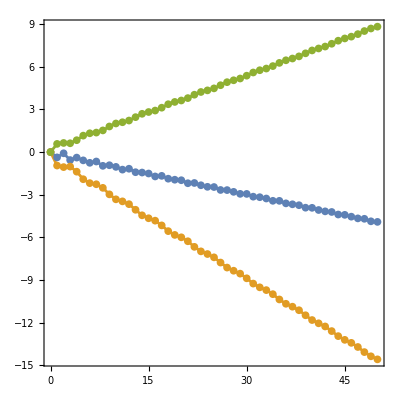

```mathematica
coin0=plusX;

θ1=π;
α1=0.39π;
ϕ1=1.3π;

θ2=3π/2;
α2=0.39π;
ϕ2=1.3π;

t=50;

G=CalculateData[coin0,θ1,α1,ϕ1,t];
H=CalculateData[coin0,θ2,α2,ϕ2,t];
J=CalculateData[coin0,{{θ1,α1,ϕ1},{θ2,α2,ϕ2}},t];

ExpValVsTimePlot[{G[[2]],H[[2]],J[[2]]},t,PlotLegends->{"","",""}]
```

```mathematica
ExpValVsTimeManipulate[coin0_,tmax_Integer]:=Manipulate[Module[{posProb,expecVal},
posProb=PosProbDisTime[coin0,θ,α,ϕ,t];
expecVal=ExpecValue[posProb,t];
ExpValVsTimePlot[expecVal,t]
],
{θ,0,2 Pi,Appearance->"Labeled"},
{α,0,Pi,Appearance->"Labeled"},
{ϕ,0,2 Pi,Appearance->"Labeled"}
]
```

```mathematica
ExpValVsTimeManipulate[coin0_,tmax_Integer,θi_:0,αi_,ϕi_]:=Manipulate[Module[{posProb,expecVal},
posProb=PosProbDisTime[coin0,θ,α,ϕ,t];
expecVal=ExpecValue[posProb,t];
ExpValVsTimePlot[expecVal,t]
],
{{θ,θi},0,2 Pi,Appearance->"Labeled"},
{{α,αi},0,Pi,Appearance->"Labeled"},
{{ϕ,ϕi},0,2 Pi,Appearance->"Labeled"}
]
```

### Valor de expectación para un tiempo fijo

```mathematica
ClearAll@FixedTimeExpValPlot
```

```mathematica
FixedTimeExpValPlot[data_List,fixedt_Integer,initCoinState_,θ_,nα_Integer,nϕ_Integer,opts:OptionsPattern[ListDensityPlot]]:=Module[{alphaTicks,phiTicks,alphaVals,phiVals,alphaLines,phiLines},
(*Extraer valores únicos y ordenarlos*)
alphaVals=Sort@DeleteDuplicates[data[[All,1]]];
phiVals=Sort@DeleteDuplicates[data[[All,2]]];

(*Calcular líneas intermedias entre valores:fronteras de celdas*)
alphaLines=MovingAverage[alphaVals,2]//Flatten;
phiLines=MovingAverage[phiVals,2]//Flatten;

(*Ticks en múltiplos de π/10 y π/5*)
alphaTicks=Table[{2*i π/nα,ToString[TraditionalForm[2*i π/nα]]},{i,0,nα}];
phiTicks=Table[{2*i*2π/nϕ,ToString[TraditionalForm[2*i*2π/nϕ]]},{i,0,nϕ}];

ListDensityPlot[data,
FrameLabel->{"α","ϕ"},
FrameTicks->{{phiTicks,None},{alphaTicks,None}},
ColorFunction->(ColorData["Rainbow"][Rescale[#,{-10,10}]]&),
ColorFunctionScaling->False,
PlotRange->All,
PlotLegends->BarLegend[{ColorData[{"Rainbow",{-10,10}}][#]&,{-10,10}}],
InterpolationOrder->0,
ImageSize->200,
Epilog->{Table[{Black,Thin,Line[{{x,Min[phiVals]},{x,Max[phiVals]}}]},{x,alphaLines}],(*Líneas verticales*)
Table[{Black,Thin,Line[{{Min[alphaVals],y},{Max[alphaVals],y}}]},{y,phiLines}](*Líneas horizontales*)
}//Flatten,
PlotLabel->Row[{"c_0 = ",LabelCoinState[initCoinState],"     θ = ",θ,",     = ",fixedt}],
opts
]
]
```

```mathematica
FixedTimeExpValPlot[data_List,fixedt_Integer,initCoinState_,θ_,nα_Integer,nϕ_Integer,αLabels_Integer,ϕLabels_Integer,opts:OptionsPattern[ListDensityPlot]]:=Module[{alphaTicks,phiTicks,alphaVals,phiVals,alphaLines,phiLines},
(*Extraer valores únicos y ordenarlos*)
alphaVals=Sort@DeleteDuplicates[data[[All,1]]];
phiVals=Sort@DeleteDuplicates[data[[All,2]]];

(*Calcular líneas intermedias entre valores:fronteras de celdas*)
alphaLines=MovingAverage[alphaVals,2]//Flatten;
phiLines=MovingAverage[phiVals,2]//Flatten;

(*Ticks en múltiplos de π/10 y π/5*)
alphaTicks=Table[{αLabels*i π/nα,ToString[TraditionalForm[αLabels*i π/nα]]},{i,0,nα}];
phiTicks=Table[{ϕLabels*i*2π/nϕ,ToString[TraditionalForm[ϕLabels*i*2π/nϕ]]},{i,0,nϕ}];

ListDensityPlot[data,
FrameLabel->{"α","ϕ"},
FrameTicks->{{phiTicks,None},{alphaTicks,None}},
ColorFunction->(ColorData["Rainbow"][Rescale[#,{-10,10}]]&),
ColorFunctionScaling->False,
PlotRange->All,
PlotLegends->BarLegend[{ColorData[{"Rainbow",{-10,10}}][#]&,{-10,10}}],
InterpolationOrder->0,
ImageSize->200,
Epilog->{Table[{Black,Thin,Line[{{x,Min[phiVals]},{x,Max[phiVals]}}]},{x,alphaLines}],(*Líneas verticales*)
Table[{Black,Thin,Line[{{Min[alphaVals],y},{Max[alphaVals],y}}]},{y,phiLines}](*Líneas horizontales*)
}//Flatten,
PlotLabel->Row[{"c_0 = ",LabelCoinState[initCoinState],"     θ = ",θ,",     = ",fixedt}],
opts
]
]
```

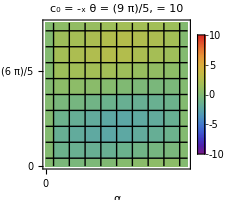

```mathematica
coin0=minusX;
θ=9π/5;
nα=10;
nϕ=10;
t=10;
fixedt=10;
res=VaryingAlpha[coin0,θ,nα,nϕ,t];
data=ExtractDataExpVal[res,fixedt];
FixedTimeExpValPlot[data,fixedt,coin0,θ,nα,nϕ]
```

### Marcar el punto en la esfera de Bloch

```mathematica
PolarPoint[{r_,polar_,azimutal_}]:=Point[r*{Sin[polar] Cos[azimutal],Sin[polar] Sin[azimutal],Cos[polar]}]
```

```mathematica
ClearAll@SphereGraph
```

```mathematica
SphereGraph[data_List,initCoinState_,θ_,opts:OptionsPattern[Graphics3D]]:=Module[{sphere},
sphere=Graphics3D[{
Opacity[0.95],Glow[SphereColor],Black,Sphere[],
Opacity[1],PointSize[0.03],

Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{1.2,0,0}}],
Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{0,1.2,0}}],
Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{0,0,1.2}}],

Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{-1.2,0,0}}],
Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{0,-1.2,0}}],
Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{0,0,-1.2}}],

Text[Style["",14,Black],{1.3,0,0}],
Text[Style["",14,Black],{0,1.3,0}],
Text[Style["",14,Black],{0,0,1.3}],

RGBColor["#00D52C"],Table[PolarPoint[{1,p[[1]],p[[2]]}],{p,Select[data,#[[3]]=="Ganadora"&]}],
Red,Table[PolarPoint[{1,p[[1]],p[[2]]}],{p,Select[data,#[[3]]=="Perdedora"&]}],
Black,Table[PolarPoint[{1,p[[1]],p[[2]]}],{p,Select[data,#[[3]]=="Indefinido"&]}],
Gray,Table[PolarPoint[{1,p[[1]],p[[2]]}],{p,Select[data,#[[3]]=="No se puede determinar"&]}]
},
Boxed->False,
PlotLabel->Row[{"c_0 = ",LabelCoinState[initCoinState],",    θ = ",θ}],
opts
]
]
```

```mathematica
coin0=minusX;
θ=9π/5;
nα=10;
nϕ=10;
t=10;
res=VaryingAlpha[coin0,θ,nα,nϕ,t];
data=ExtractDataSphereGraph[res];
SphereGraph[data,coin0,θ]
```

-Graphics3D-

### Valor de expectación contra θ

```mathematica
ClearAll@ExpValVsThetaPlot
```

```mathematica
ExpValVsThetaPlot[coin0_,α_,ϕ_,tmax_Integer]:=Module[{thetaVals,expecVals},
thetaVals=Subdivide[0,2 π,100];

expecVals=Table[Table[ExpecValue[PosProbDisTime[coin0,θ,α,ϕ,t],t][[t+1]],{θ,thetaVals}],{t,1,tmax}];

ListLinePlot[Transpose[{thetaVals,#}]&/@expecVals,
PlotLegends->Placed[LineLegend[Range[1,tmax],
LabelStyle->{FontSize->12},
LegendLabel->Style["",FontSize->13]],
Right
],
Frame->True,
FrameLabel->{"",""},
FrameTicks->{{Automatic,Automatic},{Table[{k π/4,ToString[TraditionalForm[k π/4]]},{k,0,8}],Automatic}},
PlotRange->{All,{-(t+0.05t),tmax+0.05tmax}},
PlotStyle->ColorData[97]/@Range[tmax],
ImageSize->Large]
]
```

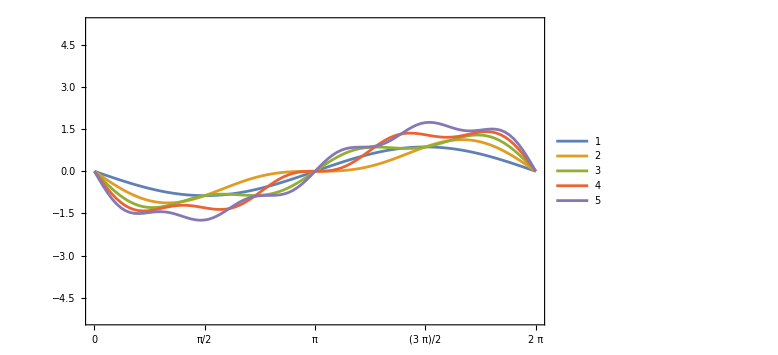

```mathematica
coin0=plusX;
α=π/2.;
ϕ=π/3.;
t=5;

ExpValVsThetaPlot[coin0,α,ϕ,t]
```

```mathematica
ExpValVsThetaPlot[coin0_,α_,ϕ_,times_List]:=Module[{thetaVals,expecVals,maxT},
thetaVals=Subdivide[0,2 π,100];

expecVals=Table[Table[ExpecValue[PosProbDisTime[coin0,θ,α,ϕ,t],t][[t+1]],{θ,thetaVals}],{t,times}];
maxT=Max[times];

ListLinePlot[Transpose[{thetaVals,#}]&/@expecVals,
PlotLegends->Placed[LineLegend[times,
LabelStyle->{FontSize->12},
LegendLabel->Style["",FontSize->13]],
Right
],
Frame->True,
FrameLabel->{"",""},
FrameTicks->{{Automatic,Automatic},{Table[{k π/4,ToString[TraditionalForm[k π/4]]},{k,0,8}],Automatic}},
PlotRange->{All,{-(maxT+0.05 maxT),maxT+0.05 maxT}},
PlotStyle->ColorData[97]/@Range[Length[times]],
ImageSize->Large]
]
```

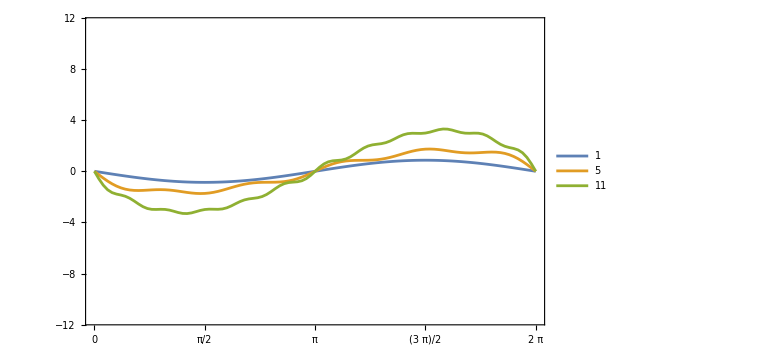

```mathematica
coin0=plusX;
α=π/2.;
ϕ=π/3.;
t={1,5,11};

ExpValVsThetaPlot[coin0,α,ϕ,t]
```

```mathematica
ClearAll@ExpValVsThetaManipulate
```

```mathematica
ExpValVsThetaManipulate[coin0_,tmax_Integer:5]:=Manipulate[
ExpValVsThetaPlot[coin0,α,ϕ,tmax],
{α,0,π,Appearance->"Labeled"},
{ϕ,0,2 π,Appearance->"Labeled"}
]
```

```mathematica
ExpValVsThetaManipulate[coin0_,tmax_Integer:5,αi_,ϕi_]:=Manipulate[
ExpValVsThetaPlot[coin0,α,ϕ,tmax],
{{α,αi},0,π,Appearance->"Labeled"},
{{ϕ,ϕi},0,2 π,Appearance->"Labeled"}
]
```

```mathematica
coin0=plusX;
t=5;
αi=π/2.;
ϕi=π/3.;
ExpValVsThetaManipulate[coin0,t]
```

```mathematica
ExpValVsThetaManipulate[coin0_,times_List]:=Manipulate[
ExpValVsThetaPlot[coin0,α,ϕ,times],
{α,0,π,Appearance->"Labeled"},
{ϕ,0,2 π,Appearance->"Labeled"}
]
```

```mathematica
ExpValVsThetaManipulate[coin0_,times_List,αi_,ϕi_]:=Manipulate[
ExpValVsThetaPlot[coin0,α,ϕ,times],
{{α,αi},0,π,Appearance->"Labeled"},
{{ϕ,ϕi},0,2 π,Appearance->"Labeled"}
]
```

```mathematica
coin0=plusX;
t={5,10};
αi=π/2.;
ϕi=π/3.;
ExpValVsThetaManipulate[coin0,t]
```

### Valor de expectación contra θ promediado en el tiempo

```mathematica
AvrgExpValVsThetaPlot[coin0_,α_,ϕ_,tmax_Integer]:=Module[{thetaVals,expecVals},
thetaVals=Subdivide[0,2 π,100];

expecVals=Table[Table[ExpecValue[PosProbDisTime[coin0,θ,α,ϕ,t],t][[t+1]],{θ,thetaVals}]/t,{t,1,tmax}];

ListLinePlot[Transpose[{thetaVals,#}]&/@expecVals,
PlotLegends->Placed[LineLegend[Range[1,tmax],
LabelStyle->{FontSize->12},
LegendLabel->Style["",FontSize->13]],
Right
],
Frame->True,
FrameLabel->{"",""},
FrameTicks->{{Automatic,Automatic},{Table[{k π/4,ToString[TraditionalForm[k π/4]]},{k,0,8}],Automatic}},
PlotRange->{All,{-(t+0.05t),tmax+0.05tmax}},
PlotStyle->ColorData[97]/@Range[tmax],
ImageSize->Large]
]
```

```mathematica
AvrgExpValVsThetaManipulate[coin0_,tmax_Integer:5]:=Manipulate[
AvrgExpValVsThetaPlot[coin0,α,ϕ,tmax],
{α,0,π,Appearance->"Labeled"},
{ϕ,0,2 π,Appearance->"Labeled"}
]
```

### Diagramas de fase

```mathematica
L[θ_,θa_,θb_]:=θa<=Mod[θ,2 Pi]<=θb;
W[θ_,θa_,θb_]:=Mod[θ,2 Pi]<=θa||Mod[θ,2 Pi]>=θb;
```

```mathematica
PhaseDiagramPlot[θa_,θb_,α_,ϕ_,β0_,γ0_]:=Module[{fs,fsf},
fs=17;fsf=20;

RegionPlot[{
L[x1,θa,θb]&&L[x2,θa,θb]&&W[x1+x2,θa,θb],
W[x1,θa,θb]&&W[x2,θa,θb]&&L[x1+x2,θa,θb],
W[x1,θa,θb]&&W[x2,θa,θb]&&W[x1+x2,θa,θb],
L[x1,θa,θb]&&L[x2,θa,θb]&&L[x1+x2,θa,θb],(L[x1,θa,θb]&&W[x2,θa,θb]&&W[x1+x2,θa,θb])||(W[x1,θa,θb]&&L[x2,θa,θb]&&W[x1+x2,θa,θb]),(L[x1,θa,θb]&&W[x2,θa,θb]&&L[x1+x2,θa,θb])||(W[x1,θa,θb]&&L[x2,θa,θb]&&L[x1+x2,θa,θb])
},
{x1,0,2 π},{x2,0,2 π},
PlotRange->{{-0.,2Pi+0.},{-0.,2Pi+0.}},
PlotPoints->50,
FrameLabel->{Style["",FontSize->fsf],Style["",FontSize->fsf]},
FrameTicks->{Table[{k,TraditionalForm[k]},{k,0,2π,π/2}],Table[{k,TraditionalForm[k]},{k,0,2π,π/2}]},
FrameStyle->Directive[Black,FontSize->fs],
GridLines->Automatic,
ImageSize->550,
PlotLabel->Style[Row[{" ", NumberForm[α/π,{Infinity,3}],
 " ",NumberForm[ϕ/π,{Infinity,3}], ",","    ",NumberForm[β0/π,{Infinity,3}]," ",
NumberForm[γ0/π,{Infinity,3}],""}],
FontSize->fs
],
PlotLegends->SwatchLegend[Automatic,{"LL=W","WW=L","WW=W","LL=L","LW=W","LW=L"},
LegendMarkerSize->20
]
]
]
```

## Resultados

## Ejemplo de José

```mathematica
coin0=QubitState[0.399π,0.169π];
t=100;
θi=0;
αi=0.82π;
ϕi=0.;
ExpValVsTimeManipulate[coin0,t,θi,αi,ϕi]
```

2.4, 4.9

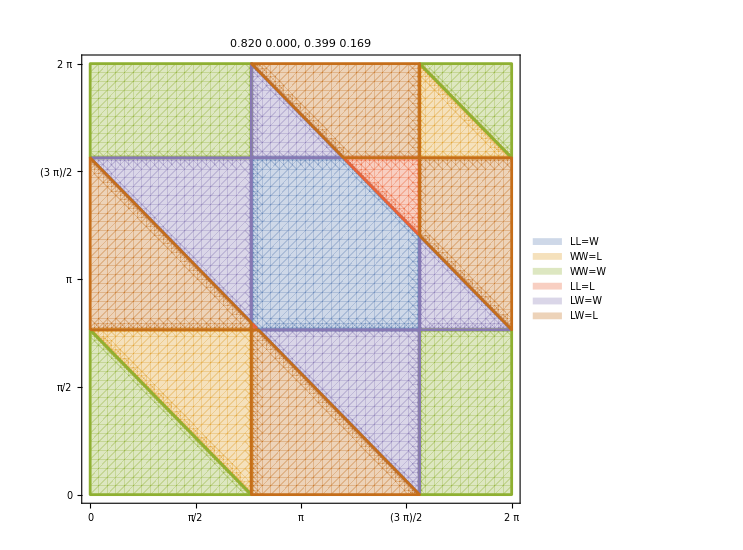

```mathematica
PhaseDiagramPlot[2.403,4.91,0.82π,0.,0.399π,0.169π]
```

## Estados importantes

### 0

Fijando α, las curvas son iguales para todo ϕ.

```mathematica
coin0=state0;
t=5;
ExpValVsThetaManipulate[coin0]
```

General::prng: Value of option PlotRange -> {{All,All},{{-5.25,-10.5},5.25}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

```mathematica
coin0=state0;
t=5;
AvrgExpValVsThetaManipulate[coin0]
```

General::prng: Value of option PlotRange -> {{All,All},{{-5.25,-10.5},5.25}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

### 1

```mathematica
coin0=state1;
t=5;
ExpValVsThetaManipulate[coin0]
```

### +_x

```mathematica
coin0=plusX;
t=5;
ExpValVsThetaManipulate[coin0]
```

General::prng: Value of option PlotRange -> {{All,All},{{-5.25,-10.5},5.25}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

```mathematica
coin0=plusX;
t=5;
AvrgExpValVsThetaManipulate[coin0]
```

General::prng: Value of option PlotRange -> {{All,All},{{-5.25,-10.5},5.25}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

### -_x

```mathematica
coin0=minusX;
t=5;
ExpValVsThetaManipulate[coin0]
```

### +_y

```mathematica
coin0=plusY;
t=5;
ExpValVsThetaManipulate[coin0]
```

### -_y

```mathematica
coin0=minusY;
t=5;
ExpValVsThetaManipulate[coin0]
```

## Plano

```mathematica
π/2.
```

1.5708

Todas ganadoras

```mathematica
coin0=QubitState[π/4., π/2.];
t=5;
AvrgExpValVsThetaManipulate[coin0,t]
```

General::prng: Value of option PlotRange -> {{All,All},{{-5.25,-10.5},5.25}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

```mathematica
coin0=QubitState[π/4., π/2.];
t=5;
αi=1.5708;
ϕi=5.07887;
ExpValVsThetaManipulate[coin0,t,αi,ϕi]
```

```mathematica
coin0=QubitState[π/4., π/2.];
t=100;
αi=1.5708;
ϕi=5.07887;
ExpValVsTimeManipulate[coin0,t,θi,αi,ϕi]
```

3.76991, 4.39823

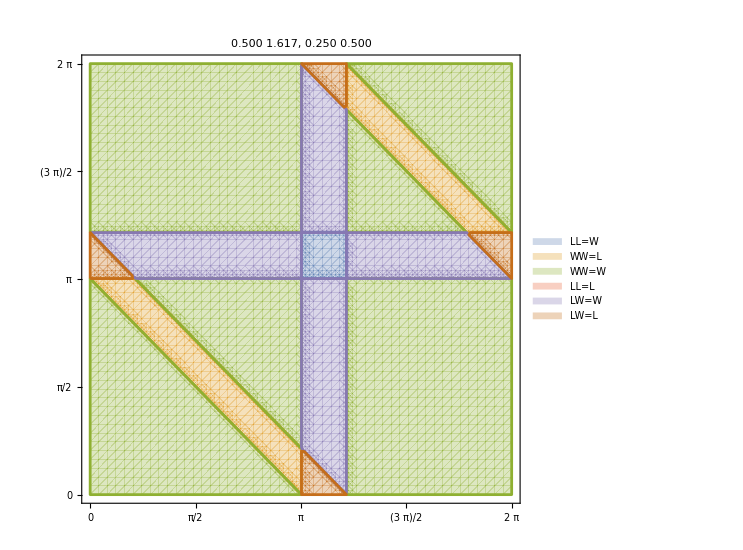

```mathematica
PhaseDiagramPlot[3.15,3.82,1.5708,5.07887,π/4.,π/2.]
```

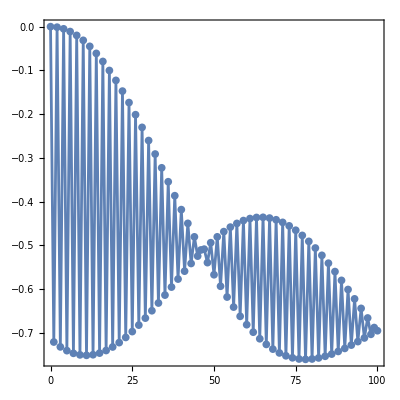

```mathematica
coin0=QubitState[π/4., π/2.];

θ=3.2;
α=1.5708;
ϕ=5.07887;

t=100;

r=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[r[[2]],t]
```

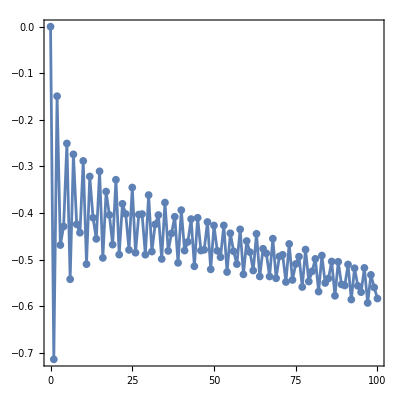

```mathematica
coin0=QubitState[π/4., π/2.];

θ=3.8;
α=1.5708;
ϕ=5.07887;

t=100;

r=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[r[[2]],t]
```

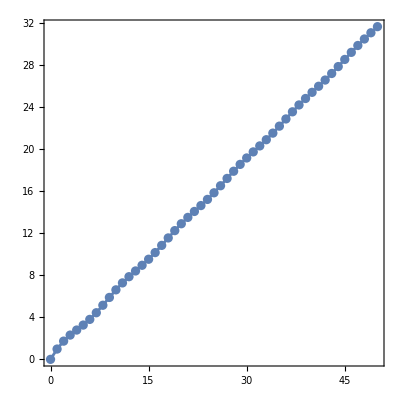

```mathematica
coin0=QubitState[π/4., π/2.];

θ1=3.2;
α1=1.5708;
ϕ1=5.07887;

θ2=3.8;
α2=α1;
ϕ2=ϕ2;

t=50;

r=CalculateData[coin0,{{θ1,α1,ϕ1},{θ2,α2,ϕ2}},t];
ExpValVsTimePlot[r[[2]],t]
```

```mathematica
coin0=QubitState[π/4., π/2.];
t=150;
αi=1.5708;
ϕi=5.07887;
ExpValVsTimeManipulate[coin0,t,αi,ϕi]
```

3.76991, 4.39823

```mathematica
coin0=QubitState[3π/4., π/2.];
t=5;
αi=1.72788;
ϕi=1.84726;
ExpValVsThetaManipulate[coin0,t,αi,ϕi]
```

General::prng: Value of option PlotRange -> {{All,All},{{-5.25,-105.},5.25}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

```mathematica
coin0=QubitState[3π/4., 3π/2.];
t=5;
αi=1.72788;
ϕi=1.84726;
ExpValVsThetaManipulate[coin0,t,αi,ϕi]
```

General::prng: Value of option PlotRange -> {{All,All},{{-5.25,-105.},5.25}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

```mathematica
coin0=QubitState[3π/4., 3π/2.];
t=1;
θi=1.23;
αi=1.72788;
ϕi=1.84726;
ExpValVsTimeManipulate[coin0,t,θi,αi,ϕi]
```

```mathematica
coin0=QubitState[3π/4., 3π/2.];
t=2;
θi=1.23;
αi=1.72788;
ϕi=1.84726;
ExpValVsTimeManipulate[coin0,t,θi,αi,ϕi]
```

```mathematica
coin0=QubitState[3π/4., 3π/2.];
t=3;
θi=1.82;
αi=1.72788;
ϕi=1.84726;
ExpValVsTimeManipulate[coin0,t,θi,αi,ϕi]
```

```mathematica
coin0=QubitState[3π/4., 3π/2.];
t=4;
θi=1.75;
αi=1.72788;
ϕi=1.84726;
ExpValVsTimeManipulate[coin0,t,θi,αi,ϕi]
```

```mathematica
coin0=QubitState[3π/4., 3π/2.];
t=5;
θi=1.7;
αi=1.72788;
ϕi=1.84726;
ExpValVsTimeManipulate[coin0,t,θi,αi,ϕi]
```

```mathematica
coin0=QubitState[π/4., 3π/2.];
t=5;
ExpValVsThetaManipulate[coin0,t]
```

## Plano

```mathematica
coin0=QubitState[π/4.,0];
t=5;
ExpValVsThetaManipulate[coin0]
```

```mathematica
coin0=QubitState[π/4., 0.];
t=5;
ExpValVsThetaManipulate[coin0]
```

```mathematica
coin0=QubitState[3π/4., π/1.];
t=5;
ExpValVsThetaManipulate[coin0]
```

```mathematica
coin0=QubitState[π/4., π/1.];
t=5;
ExpValVsThetaManipulate[coin0]
```

## Plano

```mathematica
coin0=QubitState[π/2., π/4.];
t=5;
ExpValVsThetaManipulate[coin0]
```

General::prng: Value of option PlotRange -> {{All,All},{{-5.25,-10.5},5.25}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

```mathematica
coin0=QubitState[π/2., 3π/4.];
t=5;
ExpValVsThetaManipulate[coin0]
```

```mathematica
coin0=QubitState[π/2., 5π/4.];
t=5;
ExpValVsThetaManipulate[coin0]
```

```mathematica
coin0=QubitState[π/2., 7π/4.];
t=5;
ExpValVsThetaManipulate[coin0]
```